## Brian — PS 14 — 2025-03-28 — Solution

## EIWL3 Sections 35 and 36

## Exercises from EIWL3 Section 35

```mathematica
(* 35.1 *) Interpreter["Location"]["Eiffel Tower"]
```

GeoPosition[{48.8583,2.29444}]

```mathematica
(* 35.2 *) Interpreter["University"]["U of T"]
```

University of Toronto

```mathematica
(* 35.3 *) Interpreter["Chemical"][{"C2H4", "C2H6", "C3H8"}]
```

{ethylene,ethane,propane}

```mathematica
(* 35.4 *) Interpreter["Date"]["20140108"]
```

Wed 8 Jan 2014

```mathematica
(* 35.5 *)  (* I was able to get this far: *)
Interpreter["University"][Table[StringJoin["U of ",letter],{letter,Capitalize[Alphabet[]]}]]
(* See below *)
```

{Failure[…],University of Birjand,University of California-Berkeley,Failure[…],The University of Edinburgh,Failure[…],University of Georgia,University of Houston,University of Illinois at Urbana-Champaign,Failure[…],Failure[…],University of Lethbridge,University of Michigan-Ann Arbor,Failure[…],Failure[…],University of Phoenix-Online Campus,Failure[…],University of Regina,University of Saskatchewan,University of Toronto,Failure[…],Failure[…],Failure[…],Failure[…],Failure[…],Failure[…]}

```mathematica
(* Then I had to look up how to proceed. The trick is to wrap *)
(* the results in Cases[ ... , _Entity]. This eliminates all *)
(* the failures. *)
Cases[Interpreter["University"][Table[StringJoin["U of ",letter],{letter,Capitalize[Alphabet[]]}]],_Entity]
```

{University of Birjand,University of California-Berkeley,The University of Edinburgh,University of Georgia,University of Houston,University of Illinois at Urbana-Champaign,University of Lethbridge,University of Michigan-Ann Arbor,University of Phoenix-Online Campus,University of Regina,University of Saskatchewan,University of Toronto}

```mathematica
(* 35.6 *)CommonName/@Cases[Interpreter["Movie"][CommonName/@EntityClass["AdministrativeDivision","AllUSStatesPlusDC"][EntityProperty["AdministrativeDivision","CapitalCity"]]],_Entity]
```

{Phoenix,Honolulu,Topeka,Annapolis,Lincoln,Santa Fe,Expedition: Bismarck,Columbus,Providence,Nashville,Olympia,Madison,Cheyenne}

```mathematica
(* 35.7 *) Cases[Interpreter["City"][StringJoin/@Permutations[{"a","i","l","m"}]],_Entity]
```

{Alim,Amli,Balm,Ilam,Lami,Lima,Lamai,Mali,Milah,Mali}

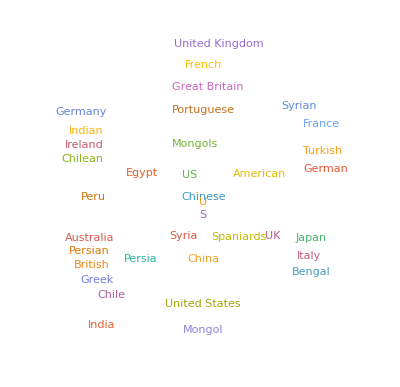

```mathematica
(* 35.8 *) WordCloud[TextCases[WikipediaData["gunpowder"],"Country"]]
```

```mathematica
(* 35.9 *) TextCases["She sells seashells by the sea shore.", "Noun"]
```

{seashells,sea,shore}

```mathematica
StringTake[WikipediaData["computers"],1000]
```

A computer is a machine that can be programmed to automatically carry out sequences of arithmetic or logical operations (computation). Modern digital electronic computers can perform generic sets of operations known as programs. These programs enable computers to perform a wide range of tasks. The term computer system may refer to a nominally complete computer that includes the hardware, operating system, software, and peripheral equipment needed and used for full operation; or to a group of computers that are linked and function together, such as a computer network or computer cluster.
A broad range of industrial and consumer products use computers as control systems, including simple special-purpose devices like microwave ovens and remote controls, and factory devices like industrial robots. Computers are at the core of general-purpose devices such as personal computers and mobile devices such as smartphones. Computers power the Internet, which links billions of computers and users.

```mathematica
(* 35.10 *) Length[TextCases[StringTake[WikipediaData["computers"],1000],#]]&/@ {"Noun","Verb","Adjective"}
```

{54,23,20}

```mathematica
(* 35.11 *) TextStructure[TextSentences[WikipediaData["computers"]][[1]]]
```

A
Determinercomputer
Noun
Noun Phrase  is
Verb    a
Determinermachine
Noun
Noun Phrase    that
Wh-Determiner
Wh-Noun Phrase  can
Verb  be
Verb  programmed
Verb    to
Preposition    automatically
Adverb
Adverb Phrasecarry
Verb  out
Particle
Particle    sequences
Noun
Noun Phrase  of
Preposition      arithmetic
Adjectiveor
Conjunctionlogical
Adjective
Adjective Phraseoperations
Noun
Noun Phrase  (
Punctuation  computation
Noun
Noun Phrase)
Punctuation
Parenthetical
Noun Phrase
Prepositional Phrase
Noun Phrase
Verb Phrase
Verb Phrase
Clause
Verb Phrase
Verb Phrase
Verb Phrase
Clause
Noun Phrase
Verb Phrase.
Punctuation
Sentence

```mathematica
(* 35.12 *)Keys[Take[Reverse[Sort[Counts[TextCases[ExampleData[{"Text","AliceInWonderland"}],"Noun"]]]],10]]
```

{Rabbit,door,voice,time,Mouse,way,moment,thing,head,garden}

```mathematica
(* 35.13 *) TextStructure[TextSentences[WikipediaData["language"]][[1]],"ConstituentGraphs"]
```

{-Graphics-}

```mathematica
(* 35.14 *) Length[Flatten[TextCases[WordList[],#]]]&/@{"Noun","Verb","Adjective","Adverb"}
```

{22728,5894,7146,2824}

```mathematica
(* 35.15 *) Flatten[WordTranslation[#,"French"]& /@ IntegerName/@Range[2,10]]
```

{deux,trois,quatre,cinq,six,sept,huit,neuf,dix}

## Exercises from EIWL3 Section 36

```mathematica
(* 36.1 *) CloudPublish[Delayed[Style[RandomInteger[1000],100]]]
```

CloudObject[https://www.wolframcloud.com/obj/03213f78-7362-48cc-b78b-6bb8326ec9d7]

```mathematica
(* 36.2 *)CloudPublish[FormFunction[{"number"->"Number"},(#number)^2&]]
```

CloudObject[https://www.wolframcloud.com/obj/d386114c-bc12-4cfd-bc8a-cf7ccfbc8d44]

```mathematica
(* 36.3 *)CloudPublish[FormFunction[{"x"->"Number","y"->"Number"},#x #y&]]
```

CloudObject[https://www.wolframcloud.com/obj/09523e1a-d0d4-470a-af78-5119d93ba7ac]

```mathematica
(* 36.4 *) CloudPublish[FormFunction[{"topic"->"String"},WordCloud[TextWords[WikipediaData[#topic]]]&]]
```

CloudObject[https://www.wolframcloud.com/obj/2dc41ee4-991f-4c00-90ae-5326f3ebcfb7]

```mathematica
(* 36.5 *) (* I don't know what Wolfram meant by "repeatedly. *)CloudPublish[FormFunction[{"string"->String},Style[StringReverse[#string],100]&]]
```

CloudObject[https://www.wolframcloud.com/obj/9c0e72ee-07ea-451e-b9de-cf8be96a1226]

```mathematica
(* 36.6 *)CloudPublish[FormFunction[{"n"->Integer},Graphics[Style[RegularPolygon[#n],RandomColor[]]]&]]
```

CloudObject[https://www.wolframcloud.com/obj/308e2e50-a0fc-4377-91b2-b158036c80d5]

```mathematica
(* 36.7 *)CloudPublish[FormFunction[{"location"->Location, "count"->Integer},GeoListPlot[GeoNearest["Volcano",#location,#count]]&]]
```

CloudObject[https://www.wolframcloud.com/obj/210df29b-cf03-4d9c-9003-b343707ace1f]